```mathematica
ClearAll[soln,EQA1,EQA2,A1,A2,G1,G2,g11,g12,g22,w1];


tsub={A1->A1[t],A2->A2[t]};
EQA1=(-(-A1 G1+(3 ⅈ A1^2 Conjugate[A1] g11)/(2 w1^2)+(3 ⅈ  Conjugate[A1]^2  A2 g12)/(2 w1^2))/.tsub)+A1'[t]
EQA2=(-(-A2 G2-ⅈ A2 Δω21  +(ⅈ A1^3 g12)/(6 w1^2))/.tsub)+A2'[t]
```

G1 A1[t]-(3 ⅈ g11 A1[t]^2 Conjugate[A1[t]])/(2 w1^2)-(3 ⅈ g12 A2[t] Conjugate[A1[t]]^2)/(2 w1^2)+A1'[t]

-(ⅈ g12 A1[t]^3)/(6 w1^2)+G2 A2[t]+ⅈ Δω21 A2[t]+A2'[t]

```mathematica
M=A1[t] A1c[t]+9 A2[t]A2c[t]; (* first invariant *)
Apsub={A1'[t]->-(-(3 ⅈ g11 A1[t]^2  A1c[t])/(2 w1^2)-(3 ⅈ g12 A2[t] A1c[t]^2)/(2 w1^2)),A2'[t]->-(-(ⅈ g12 A1[t]^3)/(6 w1^2)+ⅈ Δω21 A2[t]),
A1c'[t]->(-(3 ⅈ g11 A1c[t]^2  A1[t])/(2 w1^2)-(3 ⅈ g12 A2c[t] A1[t]^2)/(2 w1^2)),A2c'[t]->(-(ⅈ g12 A1c[t]^3)/(6 w1^2)+ⅈ Δω21 A2c[t])};
Expand[D[M,t]/.Apsub]
```

0

```mathematica
Eq=   C0 A1c[t]A1[t]+C1 A2c[t] A2[t] Δω21 + C2  g11 (A1c[t]A1[t])^2+C3  g12 ( A1[t]^3 A2c[t]+A1c[t]^3A2[t]) ;
(* second invariant  *)
Eqcc=Expand[D[Eq,t]/.Apsub];
co1=Coefficient[Eqcc,A1c[t]^3 A2[t]];
co2=Coefficient[Eqcc,A1[t] A1c[t]^4 A2[t]];
co3=Coefficient[Eqcc,A1[t]^3 A2c[t]];
co4=Coefficient[Eqcc,A1[t]^4 A1c[t] A2c[t]];
csoln=Solve[{co1,co2,co3,co4}=={0,0,0,0},{C0,C1,C2,C3}];
Eq2=  Simplify[ (C0 A1c[t]A1[t]+C1 A2c[t] A2[t] Δω21 + C2  g11 (A1c[t]A1[t])^2+C3  g12 ( A1[t]^3 A2c[t]+A1c[t]^3A2[t])/.csoln)/.C0->1/.C2->1 ][[1]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

A1[t] A1c[t]+g11 A1[t]^2 A1c[t]^2-(-9+4 w1^2 Δω21) A2[t] A2c[t]+2/3 g12 (A1c[t]^3 A2[t]+A1[t]^3 A2c[t])

```mathematica
Eq2=-Simplify[C2 g11 A1[t]^2 A1c[t]^2-(4 C2 w1^2 Δω21) A2[t] A2c[t]+2/3 C2 g12 (A1c[t]^3 A2[t]+A1[t]^3 A2c[t])]/.C2->1;
Expand[D[Eq2,t]/.Apsub]
Eq3=Eq2/.{A1c[t]->Conjugate[A1[t]],A2c[t]->Conjugate[A2[t]]}
```

0

-g11 A1[t]^2 Conjugate[A1[t]]^2+4 w1^2 Δω21 A2[t] Conjugate[A2[t]]-2/3 g12 (A2[t] Conjugate[A1[t]]^3+A1[t]^3 Conjugate[A2[t]])

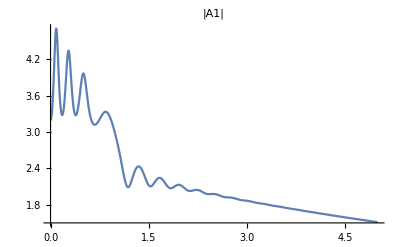

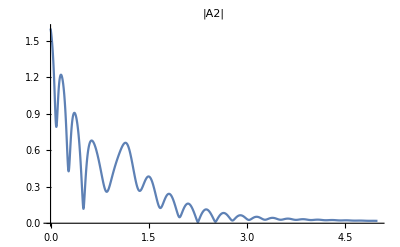

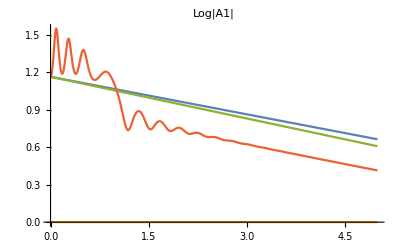

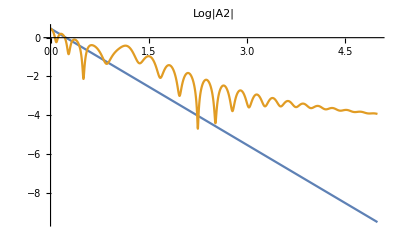

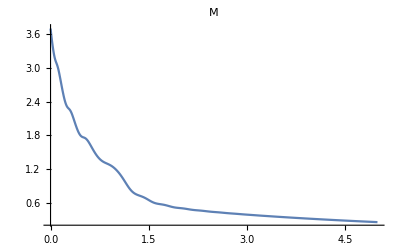

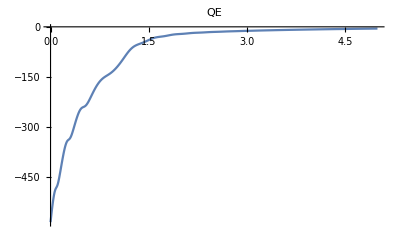

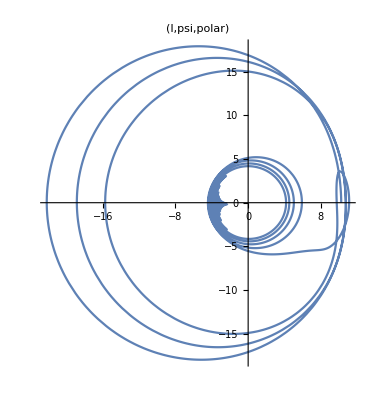

-Graphics3D-

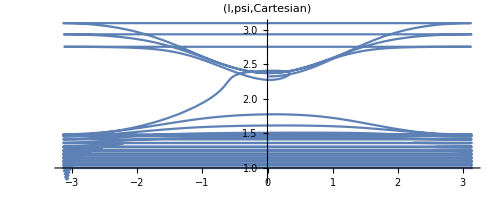

-Graphics3D-

-Graphics3D-

```mathematica
ClearAll[EOM,EOM1n, EOM2n,A1,A2,pv];
g12v=1;
g11v=1;
g22v=0;
G1v=.1;
G2v=2.;
dc1v=1;
Δω21v=-40;
Fv=0;
w1v=1;
pv={g12->g12v,g11->g11v,g22->g22v,G1->G1v,G2->G2v,Δω21->Δω21v,w1->w1v};
EOM=Chop[{EQA1,EQA2}/.pv];
EOM1n=EOM[[1]];
EOM2n=EOM[[2]];
Mn=(Abs[A1[t]]^2/9+ Abs[A2[t]]^2);
Eq3n=Eq3/.pv;

qq=0.8;
A10=qq 4;
A20=qq 2;
tmax=5;
soln=NDSolve[ {EOM1n==0,EOM2n==0,A1[0]==A10,A2[0]==A20},{A1[t],A2[t]},{t,0,tmax}];
(* ,AccuracyGoal->35,PrecisionGoal->11*)
Plot[Abs[A1[t]]/.soln,{t,0,tmax},PlotRange->All,PlotPoints->300,PlotLabel->"|A1|"]
Plot[Abs[A2[t]]/.soln,{t,0,tmax},PlotRange->All,PlotPoints->300,PlotLabel->"|A2|"]
(* Plot[{Log[Abs[A10]Exp[-G1v t]],Log[Abs[A1[t]]]/.soln},{t,0,tmax},PlotRange->All,PlotPoints->300,PlotLabel->"Log|A1|"]
Plot[{Log[Abs[A20]Exp[-G2v t]],Log[Abs[A2[t]]]/.soln},{t,0,tmax},PlotRange->All,PlotPoints->300,PlotLabel->"Log|A2|"] *)
Plot[{Log[Abs[A10]Exp[-G1v t]],0 Log[Abs[A10]Exp[-(G1v+G2v) t]],Log[Abs[A10]Exp[-(g12v/3g11v)^2 t]],Log[Abs[A1[t]]]/.soln},{t,0,tmax},PlotRange->All,PlotPoints->300,PlotLabel->"Log|A1|"]
Plot[{Log[Abs[A20]Exp[-G2v t]],Log[Abs[A2[t]]]/.soln},{t,0,tmax},PlotRange->All,PlotPoints->300,PlotLabel->"Log|A2|"]
Plot[(Mn/.soln),{t,0,tmax},PlotRange->All,PlotPoints->300,PlotLabel->"M"]
Plot[(Eq3n/.soln),{t,0,tmax},PlotRange->All,PlotPoints->300,PlotLabel->"QE"]
ParametricPlot[{Abs[A1[t]]^2 Cos[3 Arg[A1[t]]-Arg[A2[t]]],Abs[A1[t]]^2 Sin[3 Arg[A1[t]]-Arg[A2[t]]]}/.soln,{t,0,tmax},PlotRange->All,PlotPoints->300,PlotLabel->"(I,psi,polar)"]
ParametricPlot3D[{Abs[A1[t]]^2 Cos[3 Arg[A1[t]]-Arg[A2[t]]],Abs[A1[t]]^2 Sin[3 Arg[A1[t]]-Arg[A2[t]]],Mn}/.soln,{t,0,tmax},PlotRange->All,PlotPoints->300,PlotLabel->"(I,psi,M, polar)"]
ParametricPlot[{Mod[3 Arg[A1[t]]-Arg[A2[t]],2Pi,-Pi],Log[Abs[A1[t]]^2] }/.soln,{t,0,tmax},PlotRange->All,PlotPoints->300,PlotLabel->"(I,psi,Cartesian)"]
ParametricPlot3D[{Mod[3 Arg[A1[t]]-Arg[A2[t]],2Pi,-Pi],Log[Abs[A1[t]]^2] ,Mn}/.soln,{t,0,tmax},PlotRange->All,PlotPoints->300,PlotLabel->"(I,psi,M,Cartesian)"]
ParametricPlot3D[{Abs[A1[t]]^2 Cos[3 Arg[A1[t]]-Arg[A2[t]]],Abs[A1[t]]^2 Sin[3 Arg[A1[t]]-Arg[A2[t]]],Eq3n}/.soln,{t,0,tmax},PlotRange->All,PlotPoints->300,PlotLabel->"(I,psi,QE)"]
```